```mathematica
S[α_]:=({{1, 0}, {α, 1}}); A=({{0, -ⅈ}, {-ⅈ, 0}}); W[a_]:=({{Exp[a], 0}, {0, Exp[-a]}});(*Stokes, Antistokes and phase operatoes*)
Q[a_,b_,x_]:=Function[z,FullSimplify[(b-a^2/4-D[a,x]/2)/.x->z]];(*From f''+af'+bf==0 to y''+Qy==0*)
U[Q_,g_,x_]:=Function[z,FullSimplify[(Q[g] D[g,x]^2-3/4(D[g,{x,2}]/D[g,x])^2+1/2(D[g,{x,3}]/D[g,x]))/.x->z]];(*From f''+Qf==0 to y''+Uy==0 with variable exchange*)
line[a_,b_]:=Function[t,a+(b-a)t];
```

```mathematica
StokesGraph[Q_]:=
Module[{zeros,poles,z,x,y,i,zerosPlot,polesPlot,plotRange,stokes, antistokes,l=0.2},
zeros=NSolve[Q[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];
zerosPlot=ListPlot[Table[{Re[zeros⟦i⟧],Im[zeros⟦i⟧]},{i,1,Length[zeros]}],PlotStyle->Blue];

poles=NSolve[Q[z]^-1==0,z];
poles=Table[z/.poles⟦i⟧,{i,1,Length[poles]}];
polesPlot=ListPlot[Table[{Re[poles⟦i⟧],Im[poles⟦i⟧]},{i,1,Length[poles]}],PlotStyle->Red];

plotRange={{Min[Min[Re[zeros]],Min[Re[poles]]]-l,Max[Max[Re[zeros]],Max[Re[poles]]]+l},{Min[Min[Im[zeros]],Min[Im[poles]]]-l,Max[Max[Im[zeros]],Max[Im[poles]]]+l}};
stokes=StreamPlot[{Cos[-1/2 Arg[Q[x+ⅈ y]]],Sin[-1/2 Arg[Q[x+ⅈ y]]]},{x,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{y,plotRange⟦2,1⟧,plotRange⟦2,2⟧}];
antistokes=StreamPlot[{Cos[-(Arg[Q[x+ⅈ y]]+π)/2],Sin[-(Arg[Q[x+ⅈ y]]+π)/2]},{x,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{y,plotRange⟦2,1⟧,plotRange⟦2,2⟧}];
{Show[stokes,zerosPlot,polesPlot,ImageSize->Large],Show[antistokes,zerosPlot,polesPlot,ImageSize->Large]}
];
```

1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))

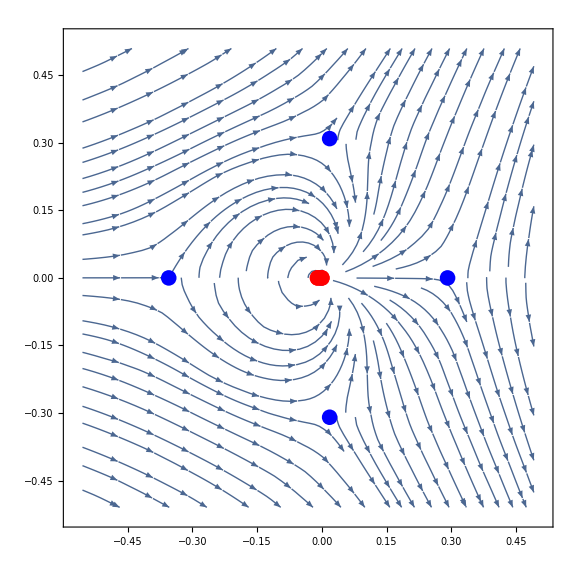
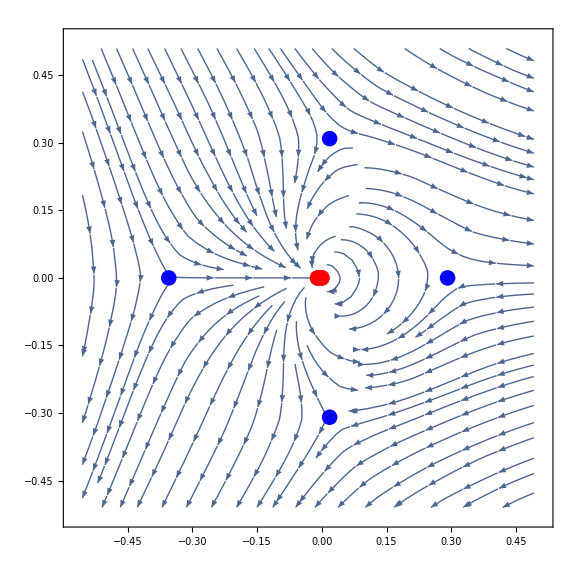

```mathematica
values={β->0.1,δ->0.1};
Q[δ^2/(x(x+δ^2)),-(x+δ^2-β^2/x+(β δ)/(x(x+δ^2))),x][x]
StokesGraph[Function[z,%/.x->z/.values]]//Quiet
Clear[values];
```